### Introduction

The geodesic equations are given below (taken from Diff. Geo. of Curves and Surfaces shamelessly):

(ⅆ^2 x^i)/(ⅆ s^2)+∑_(j,k=1)^2 (Γ^i)_jk(ⅆ x^j)/ⅆs(ⅆ x^k)/ⅆs=0   for i = 1,2

where the Christoffel symbols are the (Γ^i)_jk, which characterize the metric on the surface in question. These equations are useful for our purposes because they hold for geodesics parameterized by arc length. These are second order ordinary differential equations, so they require boundary conditions. Since there are two coordinates (x^1,x^2), we must have four boundary conditions (which we will simplify to three by assuming the first derivative has unit magnitude):

x(0)=(x^1(0),x^2(0))
x'(0)=cosθ u+sinθ v

where u,v are the unit coordinate vectors at x(0).
For now, let’s skip the difficult part of determining the geodesic parameterization in terms of arc length (either analytically or numerically) and let’s assume that we have found a parameterization for a geodesic on our coordinate map that satisfies the above equations. Since this parameterization is parameterized by arc length, we simply ‘step’ along this geodesic for one step length h:

p_(n+1)=x(h)

where x is the geodesic with x(0)=p_n

This procedure allows us to define a step length h and a random direction θ for each step in our random walk (and thus perform a random walk on any surface that we can solve the geodesic equations for)

### Plane

The Christoffel symbols are identically zero for the entire plane. This leads rather quickly to the analytical solution for geodesics of the familiar line:

x(s)=p_0+u(θ)s

where p_0 is the starting point and θ is an angle from an x-axis. Thus we have the stepping function

p_(n+1)=p_n+u(θ)h

```mathematica
planewalk[steplength_,numsteps_]:=Module[{stepfunc},
stepfunc[{x_,y_}]:=Module[{θ},
θ=RandomReal[{0,2π}];
{x+steplength*Cos[θ],y+steplength*Sin[θ]}
];
NestList[
stepfunc,
{0,0},
numsteps
]];
planehist[steplength_,numsteps_][numpts_]:=Module[{data},
data=Table[Norm[planewalk[steplength,numsteps][[-1]]],{numpts}];
Histogram[{data}]
];
```

### More General Functions

From here on, it will be easier to develop code for a more general 2D manifold and apply it to different manifolds with different coordinate maps. (Most of this code and equations are taken from [Geodesics Using Mathematica by Lewis]. The equations we will use are

u'=p
v'=q
p'=-1/(x_u·x_u)(x_uu·x_u p^2+2x_uv·x_up q+x_vv·x_u q^2)
q'=-1/(x_v·x_v)(x_uu·x_v p^2+2x_uv·x_vp q+x_vv·x_v q^2)

where x is the coordinate map from the u-v plane onto the 2D manifold. These equations are a system of four first order ordinary differential equations. We use a similar procedure used as in [Lewis] to translate this system of equations to Mathematica:

```mathematica
Clear[geodesicequations,nsteponce,nsteponceRANDANG,stepcheck];
geodesicequations[{x_,{umin_,umax_},{vmin_,vmax_}}][u_,v_,p_,q_]:=Module[{xu,xv,xuu,xuv,xvv},
xu=D[x[u,v],u];
xv=D[x[u,v],v];
xuu=D[xu,u];
xuv=D[xu,v];
xvv=D[xv,v];
Simplify[
{(-1/xu.xu)*(xuu.xu p^2+2xuv.xu p q+xvv.xu q^2),
(-1/xv.xv)*(xuu.xv p^2+2xuv.xv p q+xvv.xv q^2),
{umin,umax},
{vmin,vmax}}
]
];
nsteponce[geoeqn_,θ_,steplength_][{u0_:0,v0_:0}]:=Module[{urange,vrange,uu,vv,u,v},
urange=geoeqn[u,v,uu,vv][[3]];
vrange=geoeqn[u,v,uu,vv][[4]];
{uu,vv}=NDSolveValue[ 
{u''[s]==geoeqn[u[s],v[s],u'[s],v'[s]][[1]],
v''[s]==geoeqn[u[s],v[s],u'[s],v'[s]][[2]],
u[0]==u0,v[0]==v0,
u'[0]==Cos[θ],v'[0]==Sin[θ]},
{u,v},
{s,0,steplength}];
{uu[steplength],vv[steplength]} (* Mod is required to stay within the domain of the coordinate map *)
];
nsteponceRANDANG[geoeqn_,steplength_][{u0_:0,v0_:0}]:=Module[{ang},
ang=RandomReal[{0,2π}];
nsteponce[geoeqn,ang,steplength][{u0,v0}]
];
stepcheck[geoeqn_,steplength_,escaperegion_][{{u0_,v0_},t_,prev_}]:=Module[{nextpt,escaped},
nextpt=nsteponceRANDANG[geoeqn,steplength][{u0,v0}];
escaped=TrueQ[nextpt∈escaperegion];
{nextpt,t+1,escaped}
];
escapewalk[geoeqn_,steplength_,escaperegion_,maxsteps_][{u0_:0,v0_:0}]:=Module[{finalpt},
finalpt=NestWhile[
stepcheck[geoeqn,steplength,escaperegion],
{{u0,v0},0,TrueQ[{u0,v0}∈escaperegion]},
Not[#[[3]]]&,
1,
maxsteps];
finalpt[[2]] (*Returns the number of steps it took to get to the escape region*)
];
escapewalks[geoeqn_,steplength_,escaperegion_,maxsteps_][{u0_:0,v0_:0}]:=Module[{ptslist,finalstep},
ptslist=NestWhileList[
stepcheck[geoeqn,steplength,escaperegion],
{{u0,v0},0,TrueQ[{u0,v0}∈escaperegion]},
Not[#[[3]]]&,
1,
maxsteps];
finalstep=Max[ptslist[[All,2]]];
{#[[1]],steplength*(finalstep-#[[2]])}&/@ptslist
(*Returns the entire list of steps it took to get to the escape region plus the distance they have to travel to get to the escape region*)
];
```

### Plane

```mathematica
Module[{plane,planemap},
plane[u_,v_]:={u,v};
planemap={plane,{-100,100},{-100,100}};
geoplane[u_,v_,p_,q_]=geodesicequations[planemap][u,v,p,q];
escapecircles[{cx_,cy_},a_,b_]:=Module[{uu,vv},
RegionUnion[
ImplicitRegion[uu^2+vv^2≥b^2,{uu,vv}],
ImplicitRegion[(uu-cx)^2+(vv-cy)^2≤a^2,{uu,vv}]]
]
];
```

```mathematica
Table[escapewalk[geoplane,0.1,escapecircles[{0,0},1,3],1000][{2,0}]*0.1,{i,10}]
```

{9.3,23.1,10.,20.,46.9,13.7,19.4,17.6,4.3,21.7}

### Sphere

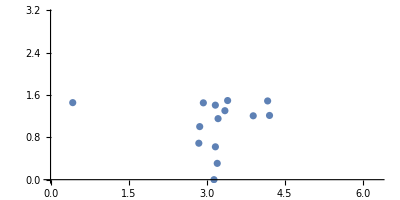

```mathematica
Module[{sphere,spheremap,geosphere,walk},
sphere[u_,v_]:={Cos[u]Cos[v],Sin[u]Cos[v],Sin[v]};
spheremap={sphere,{0,2π},{0,π}};
geosphere[u_,v_,p_,q_]=geodesicequations[spheremap][u,v,p,q];
walk=escapewalks[geosphere,π/10,
ParametricRegion[{uu,vv},{{uu,0,π/4},{vv,0,2π}}],200][{π,0}];
ListPlot[walk[[All,1]],PlotRange->{{0,2π},{0,π}},AspectRatio->1/2]
]
```

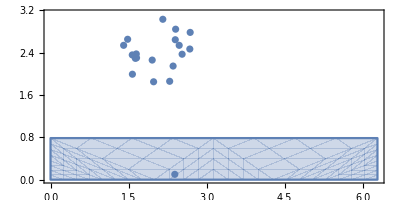

```mathematica
Module[{sphere,spheremap,geosphere,escapereg,uu,vv,eplot,pt0,walk},
sphere[u_,v_]:={Cos[u]Cos[v],Cos[v]Sin[u],Sin[v]};
spheremap={sphere,{0,2π},{0,π}};
geosphere[u_,v_,p_,q_]=geodesicequations[spheremap][u,v,p,q];
escapereg=ParametricRegion[{uu,vv},{{uu,0,2π},{vv,0,π/4}}];
eplot=RegionPlot[escapereg,PlotRange->{{0,2π},{0,π}},AspectRatio->1/2];
pt0={π,π/2};
walk=escapewalks[geosphere,π/10,escapereg,200][{π/2,3π/4}];
Show[eplot,ListPlot[walk[[All,1]]]]
]
```

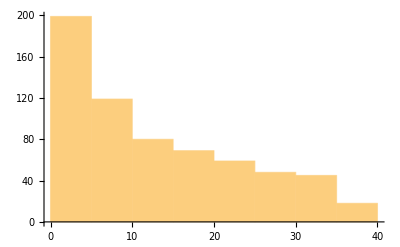

```mathematica
Module[{sphere,spheremap,geosphere,escapereg,pt0,data},
sphere[u_,v_]:={Cos[u]Cos[v],Cos[v]Sin[u],Sin[v]};
spheremap={sphere,{0,2π},{0,π}};
geosphere[u_,v_,p_,q_]=geodesicequations[spheremap][u,v,p,q];
escapereg=ParametricRegion[{uu,vv},{{uu,0,π/2},{vv,0,π/2}}];
pt0={π,π/2};
data=Flatten[Table[escapewalks[geosphere,π/10,escapereg,120][pt0][[All,2]],{30}]];
Histogram[data]
]
```

Start at south pole: (u,v)=(0,π), escape region is a circle around the north pole: 0≤u≤2π,0≤v≤v_max

```mathematica
Module[{sphere,spheremap,geosphere,pt0,escapetests,vmaxes,data},
sphere[u_,v_]:={Cos[u]Cos[v],Cos[v]Sin[u],Sin[v]};
spheremap={sphere,{0,2π},{0,π}};
geosphere[u_,v_,p_,q_]=geodesicequations[spheremap][u,v,p,q];
pt0={0,π};
escapetests[vmax_]:=Module[{escapereg},
escapereg=ParametricRegion[{uu,vv},{{uu,0,2π},{vv,0,vmax}}];
Table[escapewalk[geosphere,π/100,escapereg,1000][pt0],{200}]
];
vmaxes=Table[π/i,{i,2,20,2}];
data=escapetests/@vmaxes;
Histogram[data,500]
]
```

$Aborted

### Torus

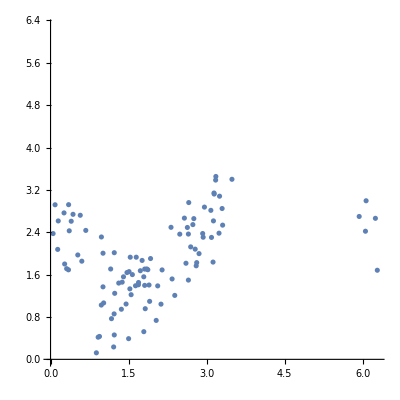

```mathematica
Module[{torus,torusmap,geotorus,walk},
torus[R_,r_][u_,v_]:={(R+r Cos[u])Cos[v],(R+r Cos[u])Sin[v],r Sin[u]};
(*R distance from center of tube to center of torus, r radius of tube, u,v∈[0,2π)*)
torusmap={torus[2,1],{0,2π},{0,2π}};
geotorus[u_,v_,p_,q_]=geodesicequations[torusmap][u,v,p,q];
walk=NestList[
nsteponceRANDANG[geotorus,π/10],
{π,π},
100];
ListPlot[walk,PlotRange->{{0,2π},{0,2π}},AspectRatio->1]
]
```

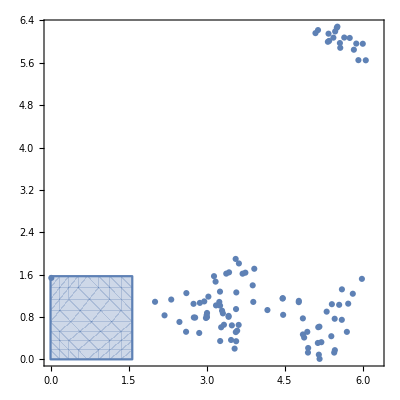

```mathematica
Module[{torus,torusmap,geotorus,escapereg,uu,vv,eplot,pt0,walk},
torus[R_,r_][u_,v_]:={(R+r Cos[u])Cos[v],(R+r Cos[u])Sin[v],r Sin[u]};
(*R distance from center of tube to center of torus, r radius of tube, u,v∈[0,2π)*)
torusmap={torus[2,1],{0,2π},{0,2π}};
geotorus[u_,v_,p_,q_]=geodesicequations[torusmap][u,v,p,q];
escapereg=ParametricRegion[{uu,vv},{{uu,0,π/2},{vv,0,π/2}}];
eplot=RegionPlot[escapereg,PlotRange->{{0,2π},{0,2π}},AspectRatio->1];
pt0={π,π/2};
walk=NestWhileList[
stepcheck[geotorus,π/10,escapereg],
{pt0,0,TrueQ[pt0∈escapereg]},
Not[#[[3]]]&,
1,
100];
Show[eplot,ListPlot[walk[[All,1]]]]
]
```

### Region Area

Chapter 6 of Diff Geo of Curves and Surfaces

```mathematica
Clear[metricdet,regionarea];
metricdet[x_][u_,v_]:=Module[{xu,xv,g},
xu=D[x[u,v],u];
xv=D[x[u,v],v];
g={{xu.xu,xu.xv},{xv.xu,xv.xv}};
Simplify[Det[g]]
];
regionarea[metdet_][region_]:=Module[{u,v},
Integrate[Sqrt[metdet[u,v]],{u,v}∈region]
];
```

```mathematica
Module[{sphere,spheremetdet,reg,u,v},
sphere[u_,v_]:={Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]};
spheremetdet[u_,v_]:=Evaluate[metricdet[sphere][u,v]];
reg=ParametricRegion[{u,v},{{u,0,2π},{v,0,π}}];
regionarea[spheremetdet][reg]
]
```

### Geodesic Distance

Re-application of the geodesic equations in a way to minimize the distance between a point and a region.

```mathematica
ClearAll[distance,geodist];
distance[geoeqn_][{u0_,v0_},{u1_,v1_}]:=Module[{uu,vv,u,v},
{uu,vv}=NDSolveValue[
{u''[t]==geoeqn[u[t],v[t],u'[t],v'[t]][[1]],
v''[t]==geoeqn[u[t],v[t],u'[t],v'[t]][[2]],
u[0]==u0,v[0]==v0,
u[1]==u1,v[1]==v1},
{u,v},
{t,0,1}];
Integrate[Sqrt[(uu'[t])^2+(vv'[t])^2],{t,0,1}]
];
geodist[geoeqn_][reg_,{u0_,v0_}]:=Module[{pt},
Minimize[distance[geoeqn][{u0,v0},pt],
pt ∈reg][[1]]
];
```

```mathematica
Module[{sphere,geosphere,reg,u,v,p,q},
sphere[u_,v_]:={Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]};
geosphere[u_,v_,p_,q_]=geodesicequations[{sphere,{0,2π},{0,π}}][u,v,p,q];
reg=ParametricRegion[{u,v},{{u,0,2π},{v,0,π}}];
distance[geosphere][{0,0},{π,0}]
]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NDSolveValue::ndnum: Encountered non-numerical value for a derivative at t == 0..

Set::shape: Lists {uu$4929,vv$4929} and NDSolveValue[{u$4929''[t]==-2 Cot[v$4929[t]] u$4929'[t] v$4929'[t],v$4929''[t]==Cos[v$4929[t]] Sin[v$4929[t]] u$4929'[t]^2,u$4929[0]==0,v$4929[0]==0,u$4929[1]==π,v$4929[1]==0},{u$4929,v$4929},{t,0,1}] are not the same shape.

∫_0^1 √(uu$4929'[t]^2+vv$4929'[t]^2)ⅆt